# Daily Study Group: Building and Applying Epidemic Models

## Vital Demographics and Age Structure

## CompartmentalModeling.wl and EpidemiologyModeling.wl

```mathematica
Get[CloudObject["https://www.wolframcloud.com/obj/rnachbar/Published/CompartmentalModeling.wl"]]
$CompartmentalModelingVersion
```

1.5 (April 26, 2021)

```mathematica
Get[CloudObject["https://www.wolframcloud.com/obj/rnachbar/Published/EpidemiologyModeling.wl"]]
$EpidemiologyModelingVersion
```

1.5 (May 3, 2021)

```mathematica
model={Transition[𝒮,β p λ[t],ℰ],Transition[ℰ,ζ,ℐ],Transition[ℐ,γ,ℛ]}
```

{𝒮→^(p β λ[t])ℰ,ℰ→^ζ ℐ,ℐ→^γ ℛ}

```mathematica
model={
𝒮(->)^(β p λ[t])ℰ,
ℰ(->)^ζ ℐ,
ℐ(->)^γ ℛ
}
```

{𝒮→^(p β λ[t])ℰ,ℰ→^ζ ℐ,ℐ→^γ ℛ}

```mathematica
modelGraph=CompartmentalModelGraph[model]
```

-Graphics-

```mathematica
CompartmentalModelGraph[model,VertexColor->{𝒮->RGBColor[0.10980392156862745, 0.6745098039215687, 0.47058823529411764],ℰ->RGBColor[1., 0.8117647058823529, 0.2823529411764706],ℐ->RGBColor[1., 0.16862745098039217, 0.16862745098039217],ℛ->RGBColor[0.12156862745098039, 0.4588235294117647, 0.996078431372549]}]//Legended[#,Placed[SwatchLegend[{RGBColor[0.10980392156862745, 0.6745098039215687, 0.47058823529411764],RGBColor[1., 0.8117647058823529, 0.2823529411764706],RGBColor[1., 0.16862745098039217, 0.16862745098039217],RGBColor[0.12156862745098039, 0.4588235294117647, 0.996078431372549]},{"susceptible","exposed","infected","recovered"}],Below]]&
```

-Graphics-

```mathematica
?DynamicTransmissionModel
```

DynamicTransmissionModel[model, t] returns an Association <|"Compartments" -> v, "ComponentTransitions" -> c, "StoichiometricMatrix" -> S, "Rates" -> r, "Equations" -> e, "TimeSymbol" -> t, "ForceOfInfection" -> f|> for the set of Transition objects in model; the argument t is the time variable. The length of the component transitions vector c may be longer than the input model because equilibria are decomposed into their forward and reverse transitions.

```mathematica
Options[DynamicTransmissionModel]//Column
```

AgeByAgeMixingSymbol→𝔐
AgeStratification→None
AgeStratifiedParameters→None
AllCauseMortalitySymbol→μ
BirthCompartments→None
Compartments→Automatic
ForceOfInfection→None
IndexPlacement→Subscript
MaleToFemaleBirthRatio→1
MortalityCompartments→None
SexStratification→None
SexStratifiedParameters→None
Stratification→None
StratifiedParameters→None
TimeSymbol→t
TotalBirthRateSymbol→Λ
CheckForIndependentComponents→True

```mathematica
modelData=DynamicTransmissionModel[model,t,ForceOfInfection->{λ,ℐ,{"Standard",Automatic}}]
```

<|Variables→{ℰ,ℐ,ℛ,𝒮},ComponentTransitions→{ℰ→^ζ ℐ,ℐ→^γ ℛ,𝒮→^(p β λ[t])ℰ},StoichiometricMatrix→{{-1,1,0,0},{0,-1,1,0},{1,0,0,-1}},Rates→{ζ ℰ[t],γ ℐ[t],p β 𝒮[t] λ[t]},Equations→{ℰ'[t]==-ζ ℰ[t]+p β 𝒮[t] λ[t],ℐ'[t]==ζ ℰ[t]-γ ℐ[t],ℛ'[t]==γ ℐ[t],𝒮'[t]==-p β 𝒮[t] λ[t]},TimeSymbol→t,ForceOfInfection→{λ[t]→ℐ[t]/(ℰ[t]+ℐ[t]+ℛ[t]+𝒮[t])}|>

```mathematica
modelData["Variables"]
```

{ℰ,ℐ,ℛ,𝒮}

```mathematica
?NextGenerationMatrix
```

NextGenerationMatrix[eqns, vars, t, forceOfInfection, infectedVars] returns the next generation matrix given a list of ODEs, a list of dependent variables, an independent variable, a list of rules for the force of infection, and a list of variables representing infected compartments. 
NextGenerationMatrix[modelDataAssociation, infectedVars] take the equations, variables, independent variable, and force of infection from the model data Association.

```mathematica
(ngm=NextGenerationMatrix[modelData,{ℰ,ℐ},DiseaseFreeEquilibrium->{𝒮->pop,ℰ->0,ℐ->0,ℛ->0}])//MatrixForm
```

((p β)/γ | (p β)/γ
0 | 0)

```mathematica
vals=Eigenvalues[ngm]
```

{(p β)/γ,0}

```mathematica
Reqn=Subscript[ℜ, 0]==Simplify[Max[Re@vals],{β,p,γ}∈PositiveReals]
```

ℜ_0==Max[0,Re[(p β)/γ]]

```mathematica
Reqn=Subscript[ℜ, 0]==(p β)/γ
```

ℜ_0==(p β)/γ

```mathematica
eqns=modelData["Equations"];
force=modelData["ForceOfInfection"]
```

{λ[t]→ℐ[t]/(ℰ[t]+ℐ[t]+ℛ[t]+𝒮[t])}

```mathematica
vars=modelData["Variables"];
varsT=Through@vars[t];
```

```mathematica
ssSoln=Solve[eqns/.force/._'[t]->0,Through[vars[t]]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{ℰ[t]→0,ℐ[t]→0}}

```mathematica
dfe={𝒮[t]->𝒩,ℰ[t]->0,ℐ[t]->0,ℛ[t]->0};
```

```mathematica
(jacobian=Outer[D,Last/@eqns/.force,varsT]//Simplify)//MatrixForm
```

(-ζ-(p β ℐ[t] 𝒮[t])/(ℰ[t]+ℐ[t]+ℛ[t]+𝒮[t])^2 | (p β 𝒮[t] (ℰ[t]+ℛ[t]+𝒮[t]))/(ℰ[t]+ℐ[t]+ℛ[t]+𝒮[t])^2 | -(p β ℐ[t] 𝒮[t])/(ℰ[t]+ℐ[t]+ℛ[t]+𝒮[t])^2 | (p β ℐ[t] (ℰ[t]+ℐ[t]+ℛ[t]))/(ℰ[t]+ℐ[t]+ℛ[t]+𝒮[t])^2
ζ | -γ | 0 | 0
0 | γ | 0 | 0
(p β ℐ[t] 𝒮[t])/(ℰ[t]+ℐ[t]+ℛ[t]+𝒮[t])^2 | -(p β 𝒮[t] (ℰ[t]+ℛ[t]+𝒮[t]))/(ℰ[t]+ℐ[t]+ℛ[t]+𝒮[t])^2 | (p β ℐ[t] 𝒮[t])/(ℰ[t]+ℐ[t]+ℛ[t]+𝒮[t])^2 | -(p β ℐ[t] (ℰ[t]+ℐ[t]+ℛ[t]))/(ℰ[t]+ℐ[t]+ℛ[t]+𝒮[t])^2)

```mathematica
vals=Eigenvalues[jacobian/.dfe]
```

{0,0,1/2 (-γ-ζ-√(γ^2+4 p β ζ-2 γ ζ+ζ^2)),1/2 (-γ-ζ+√(γ^2+4 p β ζ-2 γ ζ+ζ^2))}

if you replace β with (γ ℜ_0)/p (from the definition of ℜ_0) you can begin to make sense of it:

```mathematica
vals/.First@Solve[Reqn,β]//Simplify
```

{0,0,1/2 (-γ-ζ-√((γ-ζ)^2+4 γ ζ ℜ_0)),1/2 (-γ-ζ+√((γ-ζ)^2+4 γ ζ ℜ_0))}

```mathematica
√((γ-ζ)^2+4 γ ζ Subscript[ℜ, 0])/.Subscript[ℜ, 0]->1//Simplify[#,{ζ,γ}∈PositiveReals]&
```

√((γ+ζ)^2)

This means that the third eigenvalue will always be negative, and the last eigenvalue will be negative if and only if ℜ_0<1. That is, the disease-free equilibrium will be locally stable if and only if ℜ_0<1.

```mathematica
CountryData["India","Population"]
```

1366417756 people

```mathematica
Grid[{
{"Parameter","Value","Description","Units"},
{pop,1366417756,"Population of India","People"},
{β,12.,"Contact rate","1/People"},
{p,0.03,"Probability of transmission","Dimensionless"},
{ζ,1/2.,"1/average incubation period","1/Day"},
{γ,1/7.,"1/average infectious period","1/Day"}
},
Dividers->{{Gray,{LightGray},Gray},{Gray,Gray,{LightGray},Gray}},
Alignment->{{Center,Decimal,Left,Center},Automatic,{{1,2}->Center,{1,3}->Center}}
]
closeCellGroup[]
```

Parameter | Value | Description | Units
pop | 1366417756 | Population of India | People
β | 12. | Contact rate | 1/People
p | 0.03 | Probability of transmission | Dimensionless
ζ | 0.5 | 1/average incubation period | 1/Day
γ | 0.142857 | 1/average infectious period | 1/Day

closeCellGroup[]

```mathematica
eqns=modelData["Equations"];
vars=modelData["Variables"];
varsT=Through[vars[t]];
force=modelData["ForceOfInfection"];
params={pop->1366417756,β->12.,p->0.03,ζ->1/2.,γ->1/7.};
inits={𝒮[0]==pop-1,ℐ[0]==1,ℰ[0]==0,ℛ[0]==0};
```

```mathematica
Reqn/.params
```

ℜ_0==2.52

```mathematica
soln=First@NDSolve[{eqns,inits}/.force/.params,vars,{t,0,2 365}];
```

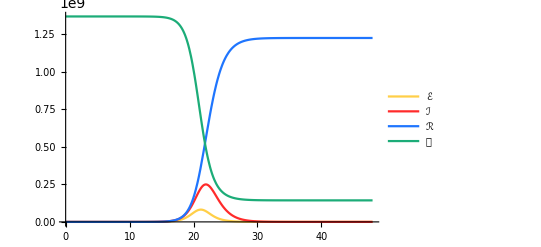

```mathematica
Plot[Through[vars[7t]]/.soln//Evaluate,{t,0,48},FrameLabel->{"time (weeks)","# people"},PlotRange->All,PlotLegends->vars,PlotStyle->{RGBColor[1., 0.8117647058823529, 0.2823529411764706],RGBColor[1., 0.16862745098039217, 0.16862745098039217],RGBColor[0.12156862745098039, 0.4588235294117647, 0.996078431372549],RGBColor[0.10980392156862745, 0.6745098039215687, 0.47058823529411764]}]
```

How many people were infected at the peak, and when did it occur?

```mathematica
FindMaximum[ℰ[t]+ℐ[t]/.soln,t]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{3.23028×10^8,{t→151.946}}

```mathematica
FindRoot[(ℰ[t]+ℐ[t])-1/.soln/.params,{t,365}]
```

{t→366.953}

### Predefined Models with EpidemiologyModelData

```mathematica
EpidemiologyModelData["Names"]
```

{cMSEIR,MSEIR,SEIAR,SEIQR,SEIR,SEIRD,SIR,SIS,SQEIQR}

```mathematica
EpidemiologyModelData["SEIAR"]
```

<|Variables→{𝒜,ℰ,ℐ,ℛ,𝒮},ComponentTransitions→{𝒜→^γ_a ℛ,ℰ→^(ζ (1-ρ))ℐ,ℰ→^(ζ ρ)𝒜,ℐ→^γ_i ℛ,𝒮→^(β λ[t])ℰ},StoichiometricMatrix→{{-1,0,0,1,0},{0,-1,1,0,0},{1,-1,0,0,0},{0,0,-1,1,0},{0,1,0,0,-1}},Rates→{γ_a 𝒜[t],ζ (1-ρ) ℰ[t],ζ ρ ℰ[t],γ_i ℐ[t],β 𝒮[t] λ[t]},Equations→{𝒜'[t]==-γ_a 𝒜[t]+ζ ρ ℰ[t],ℰ'[t]==-ζ (1-ρ) ℰ[t]-ζ ρ ℰ[t]+β 𝒮[t] λ[t],ℐ'[t]==ζ (1-ρ) ℰ[t]-γ_i ℐ[t],ℛ'[t]==γ_a 𝒜[t]+γ_i ℐ[t],𝒮'[t]==-β 𝒮[t] λ[t]},TimeSymbol→t,ForceOfInfection→{λ[t]→ℐ[t]},Description→𝒮 = susceptible, ℰ = exposed, ℐ = infectious, 𝒜 = asymptomatic, ℛ = removed; β = probability of transmission, (1 / ζ) = average incubation period, (1 / γ_i = average symptomatic infectious period, (1 / γ_a = average asymptomatic infectious period, ρ = fraction asymptomatic; mass action incidence.|>

### DynamicTransmissionModel Options for Births and Deaths

The symbol capital lambda (Λ) is traditionally used to signify the birth rate and the symbol mu (μ) to represent the death rate. The options for DynamicTransmissionModel are set up with this in mind:

```mathematica
FilterRules[Options[DynamicTransmissionModel],{TotalBirthRateSymbol,AllCauseMortalitySymbol}]
```

{AllCauseMortalitySymbol→μ,TotalBirthRateSymbol→Λ}

```mathematica
vitalModelData=DynamicTransmissionModel[model,t,ForceOfInfection->{λ,ℐ,{"Standard",Automatic}},BirthCompartments->𝒮]
```

<|Variables→{ℰ,ℐ,ℛ,𝒮},ComponentTransitions→{ℰ→^ζ ℐ,ℰ⇥^μ,ℐ→^γ ℛ,ℐ⇥^μ,ℛ⇥^μ,𝒮⇥^μ,𝒮→^(p β λ[t])ℰ,↦^Λ 𝒮},StoichiometricMatrix→{{-1,1,0,0},{-1,0,0,0},{0,-1,1,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1},{1,0,0,-1},{0,0,0,1}},Rates→{ζ ℰ[t],μ ℰ[t],γ ℐ[t],μ ℐ[t],μ ℛ[t],μ 𝒮[t],p β 𝒮[t] λ[t],Λ},Equations→{ℰ'[t]==-ζ ℰ[t]-μ ℰ[t]+p β 𝒮[t] λ[t],ℐ'[t]==ζ ℰ[t]-γ ℐ[t]-μ ℐ[t],ℛ'[t]==γ ℐ[t]-μ ℛ[t],𝒮'[t]==Λ-μ 𝒮[t]-p β 𝒮[t] λ[t]},TimeSymbol→t,ForceOfInfection→{λ[t]→ℐ[t]/(ℰ[t]+ℐ[t]+ℛ[t]+𝒮[t])}|>

### Model Compartments

The "ComponentTransitions" have been augmented with a source transition for births into the 𝒮 compartment and sink transitions from all the compartments for deaths:

```mathematica
vitalModelData["ComponentTransitions"]//Column
```

ℰ→^ζ ℐ
ℰ⇥^μ
ℐ→^γ ℛ
ℐ⇥^μ
ℛ⇥^μ
𝒮⇥^μ
𝒮→^(p β λ[t])ℰ
↦^Λ 𝒮

```mathematica
CompartmentalModelGraph[vitalModelData["ComponentTransitions"],VertexColor->{𝒮->RGBColor[0.10980392156862745, 0.6745098039215687, 0.47058823529411764],ℰ->RGBColor[1., 0.8117647058823529, 0.2823529411764706],ℐ->RGBColor[1., 0.16862745098039217, 0.16862745098039217],ℛ->RGBColor[0.12156862745098039, 0.4588235294117647, 0.996078431372549]},GraphLayout->{"LayeredEmbedding","RootVertex"->𝒮,"Orientation"->Left}]//Legended[#,Placed[SwatchLegend[{RGBColor[0.10980392156862745, 0.6745098039215687, 0.47058823529411764],RGBColor[1., 0.8117647058823529, 0.2823529411764706],RGBColor[1., 0.16862745098039217, 0.16862745098039217],RGBColor[0.12156862745098039, 0.4588235294117647, 0.996078431372549]},{"susceptible","exposed","infected","recovered"}],Right]]&
```

-Graphics-

```mathematica
vitalModelData["Equations"]//Column
```

ℰ'[t]==-ζ ℰ[t]-μ ℰ[t]+p β 𝒮[t] λ[t]
ℐ'[t]==ζ ℰ[t]-γ ℐ[t]-μ ℐ[t]
ℛ'[t]==γ ℐ[t]-μ ℛ[t]
𝒮'[t]==Λ-μ 𝒮[t]-p β 𝒮[t] λ[t]

```mathematica
varsT=Through[vitalModelData["Variables"][t]]
```

{ℰ[t],ℐ[t],ℛ[t],𝒮[t]}

```mathematica
totalPopEqn=𝒩[t]==Total[varsT]
```

𝒩[t]==ℰ[t]+ℐ[t]+ℛ[t]+𝒮[t]

```mathematica
totalPopDiffEqn=D[totalPopEqn,t]
```

𝒩'[t]==ℰ'[t]+ℐ'[t]+ℛ'[t]+𝒮'[t]

```mathematica
eqn=𝒩'[t]==0/.Rule@@totalPopDiffEqn/.Rule@@@vitalModelData["Equations"]//Simplify
```

Λ==μ (ℰ[t]+ℐ[t]+ℛ[t]+𝒮[t])

```mathematica
eqn=eqn/.Rule@@Reverse[totalPopEqn]
```

Λ==μ 𝒩[t]

```mathematica
mortSoln=First@Solve[eqn,μ]
```

{μ→Λ/𝒩[t]}

```mathematica
birthSoln=First@Solve[eqn,Λ]
```

{Λ→μ 𝒩[t]}

### Basic Reproduction Number, ℜ_0, with NextGenerationMatrix

```mathematica
(ngm=NextGenerationMatrix[vitalModelData,{ℰ,ℐ},DiseaseFreeEquilibrium->{𝒮->pop,ℰ->0,ℐ->0,ℛ->0}])//MatrixForm
```

((p β ζ)/((γ+μ) (ζ+μ)) | (p β)/(γ+μ)
0 | 0)

```mathematica
vals=Eigenvalues[ngm]
```

{0,(p β ζ)/((γ+μ) (ζ+μ))}

```mathematica
Reqn=Subscript[ℜ, 0]==Simplify[Max[Re@vals],{β,p,ζ,γ,μ}∈PositiveReals]
```

ℜ_0==Max[0,Re[(p β ζ)/((γ+μ) (ζ+μ))]]

## Age Structure

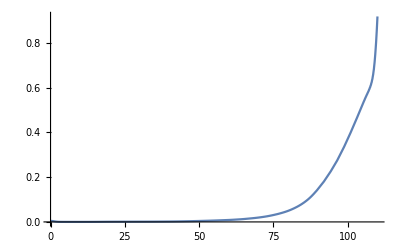

```mathematica
With[{mortalityForce=MortalityData[<|"country"->"UnitedStates","Gender"->"Any"|>,"MortalityForceDimensionless"]},Plot[mortalityForce[age],{age,0,110},PlotRange->All,FrameLabel->{"age (y)","mortality force (1/y)"}]]
```

### Age Groups

```mathematica
ageGroups=Partition[Append[Range[0,75,5],∞],2,1]
nAges=Length[ageGroups]
```

{{0,5},{5,10},{10,15},{15,20},{20,25},{25,30},{30,35},{35,40},{40,45},{45,50},{50,55},{55,60},{60,65},{65,70},{70,75},{75,∞}}

16

```mathematica
ageModel={
𝒮(->)^(p λ[t])ℰ,
ℰ(->)^ζ ℐ,
ℐ(->)^γ ℛ
};
```

```mathematica
ageModelData=DynamicTransmissionModel[ageModel,t,
ForceOfInfection->{λ,ℐ,{"Standard",Automatic}},
BirthCompartments->𝒮,
AgeStratification->{α,nAges},
AgeByAgeMixingSymbol->β
];
```

```mathematica
CompartmentalModelGraph[ageModelData["ComponentTransitions"],VertexColor->{Subscript[𝒮, _]->RGBColor[0.10980392156862745, 0.6745098039215687, 0.47058823529411764],Subscript[ℰ, _]->RGBColor[1., 0.8117647058823529, 0.2823529411764706],Subscript[ℐ, _]->RGBColor[1., 0.16862745098039217, 0.16862745098039217],Subscript[ℛ, _]->RGBColor[0.12156862745098039, 0.4588235294117647, 0.996078431372549]},GraphLayout->{"LayeredDigraphEmbedding","RootVertex"->Subscript[𝒮, 1],"Orientation"->Left},ImageSize->12 72]//Legended[#,Placed[SwatchLegend[{RGBColor[0.10980392156862745, 0.6745098039215687, 0.47058823529411764],RGBColor[1., 0.8117647058823529, 0.2823529411764706],RGBColor[1., 0.16862745098039217, 0.16862745098039217],RGBColor[0.12156862745098039, 0.4588235294117647, 0.996078431372549]},{"susceptible","exposed","infected","recovered"}],Right]]&
```

-Graphics-

```mathematica
params=<|p->0.025,ζ->1/2.,γ->1/7.|>;
```